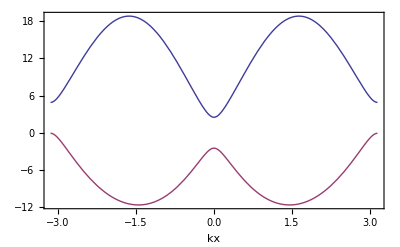

/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersiont1t2+t0.2.png

```mathematica
Clear[ϵn,t,α,ξ,μ,para,En1,En2,kx,ky];
t=0.5;para=1.20;μ=-4.8;
α=15.0;mz=2.50;ky=0.0;
ϵn[kx_,ky_]:=-2*para*(1-t)*(Cos[kx]+Cos[ky])-2*para*t*(Cos[2*kx]+Cos[2*ky])-μ;
ξ=Sqrt[α^2*(Sin[kx]^2+Sin[ky]^2)+mz^2];
En1[kx_,ky_]:=ϵn[kx,ky]+ξ;
En2[kx_,ky_]:=ϵn[kx,ky]-ξ;
Image12=Plot[{En1[kx,ky],En2[kx,ky]},{kx,-Pi,Pi},AxesLabel->Automatic,Frame->True,PlotRange->All(*FrameTicks->{{{-4,-2,-1,0,1,2,4},None},{{-4Pi,2*Pi,-Pi,0,Pi,28Pi,4 Pi},None}}*)]
Export["/home/slal2/Documents/NiveditaNotes/new/omega40/edgestates_bulkproperties/Dispersiont1t2+t0.2.png",Image12]
```